### lib

```mathematica
SetOptions[{Plot, RegionPlot, ListPlot},GridLines->Automatic];
```

```mathematica
ProjectPath="/Users/artemvorozhtsov/projects/shipit";
shipitCmd = ProjectPath <> "/shipit2";
```

```mathematica
GIndex[mean_,σ_,ksi_]:=ksi/σ^2+(ⅇ^(-mean^2/(2 σ^2)) σ)/(√(2 π))+1/2 mean (1+Erf[mean/(√2 σ)]);
MossIndex[mean_,σ_, s_,l_,psi_]:=(mean+s*σ*Sqrt[Max[psi,l+Log[σ]]]);

PIndex[mean_,σ_, s_]:=mean + s *σ;
```

```mathematica
RCndsM11[baseMean_, baseSigma_,{pShipSigmas_,pStopSigmas_,others___}]:=(
PIndex[mean,sigma,pStopSigmas] ≤  0 ||
PIndex[-mean,sigma,pShipSigmas] ≤0
);
RCndsM12[baseMean_, baseSigma_,{pShipSigmas_,pStopSigmas_,sigmaMul_,others___}]:=(
PIndex[mean,sigma,pStopSigmas] <=  PIndex[baseMean,baseSigma,pStopSigmas] ||
PIndex[-mean,sigma,pShipSigmas] <= PIndex[0,sigmaMul * baseSigma,pShipSigmas]
);
RCndsM13[baseMean_, baseSigma_,{pShipSigmas_, pStopSigmas_,others___}]:=Module[
{sigmaMul},
 sigmaMul=PIndex[baseMean, baseSigma, pStopSigmas]/pStopSigmas/ baseSigma;
RCndsM12[baseMean, baseSigma,{pShipSigmas, pStopSigmas,sigmaMul}]
];
RCndsM14[baseMean_, baseSigma_,{pStopSigmas_, pA_,others___}]:=Module[
{sigmaMul, pShipSigmas},
pShipSigmas = pStopSigmas + pA;
 sigmaMul=PIndex[baseMean, baseSigma, pStopSigmas]/pStopSigmas/ baseSigma;
RCndsM12[baseMean, baseSigma,{pShipSigmas, pStopSigmas,sigmaMul}]
];
RCndsM20[baseMean_,baseSigma_,{pS_, pL_,pShipSigmas_, pKsi_, other___}]:=Module[
{sigmaMul,baseIndexS, sigma0},
sigmaMul ;
baseIndexS=MossIndex[baseMean,baseSigma,pS,pL,pKsi]/pS;
sigma0=0.5*baseSigma;sigma0=baseIndexS/Sqrt[Max[pKsi,pL+Log[sigma0]]];
sigma0=baseIndexS/Sqrt[Max[pKsi,pL+Log[sigma0]]];
sigma0=baseIndexS/Sqrt[Max[pKsi,pL+Log[sigma0]]];
MossIndex[mean,sigma,pS,pL,pKsi] <=  MossIndex[baseMean, baseSigma,pS,pL,pKsi]||
PIndex[-mean,sigma,pShipSigmas] <= PIndex[0,sigma0,pShipSigmas]
];
RCndsM25[baseMean_,baseSigma_,{pS_, pL_, pKsi_, other___}]:=(
MossIndex[mean,sigma,pS,pL,pKsi] <=  MossIndex[baseMean, baseSigma,pS,pL,pKsi]||
MossIndex[-mean,sigma,pS,pL,pKsi] <=  MossIndex[baseMean, baseSigma,pS,pL,pKsi]
);
RCndsM30[baseMean_,baseSigma_,{pS_, pShip_, pKsi_, other___}]:=(
GIndex[mean,pS * sigma,pKsi] <=  GIndex[baseMean,pS * baseSigma,pKsi]||
GIndex[mean,pS * sigma,pKsi] *pShip <= mean
);

RCndsM32[baseMean_, baseSigma_, {pS_, pShip_,other___}]:=Module[
{pKsi}, 
pKsi=-(baseSigma*pS)^2*GIndex[baseMean,pS * baseSigma,0];
 RCndsM30[baseMean, baseSigma, {pS, pShip, pKsi}] 
];
```

```mathematica
SetSharedFunction[ShipitM];
Round6[x_]:= Round[x,10.0^-6];
SetAttributes[Round6, {Listable}];
Shipit0[args__]:=Module[
{input, result, paramsRound},
input = ((ToString[#]<>" ")&/@Flatten[{args}] )// StringJoin;
result = RunProcess[shipitCmd, All,  input];
ImportString[result["StandardOutput"],"CSV"]//Flatten
];
(* point__ = (m_,seed_, weeks_,trials_,mean_, sigma_,error_) *)
Shipit[point__, params_]:= Module[
{input, result, paramsRound, memKey},
paramsRound=Round6[params];
memKey = ToString[{point, paramsRound}];
result=ShipitM[memKey];
If[
result =!= Null && Head[result]=!=ShipitM , 
result, 
result = Shipit0[point, paramsRound];
ShipitM[memKey]= result;
result
]
]
```

### Save and load ShipitM

```mathematica
<< (ProjectPath <> "/mem_shipit.nb");
```

```mathematica
(* Save[ProjectPath<>"/mem_shipit_new.nb", ShipitM]; *)
```

### baseMean = -1; baseSigma = 1.0;

```mathematica
baseMean=-1; baseSigma=1.0;
```

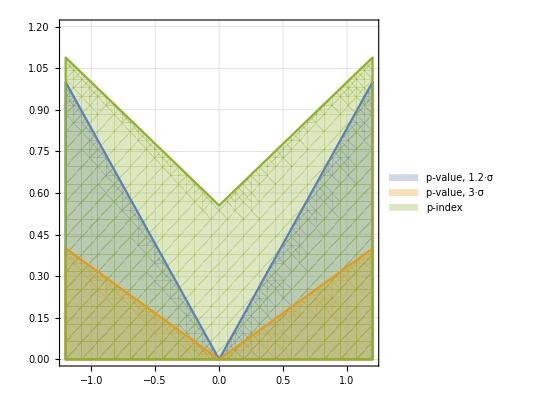

```mathematica
RegionPlot[
{
RCndsM11[baseMean, baseSigma, {1.2, 1.2}],
RCndsM11[baseMean, baseSigma, {3, 3}],
RCndsM14[baseMean, baseSigma, {2.2481, 0}]
},
{mean, -1.2, 1.2},
{sigma, 0, 1.2}, PlotLegends->{"p-value, 1.2·σ","p-value, 3·σ","p-index"}
]
```

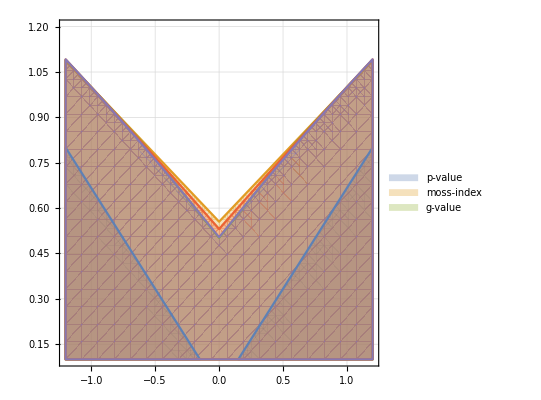

```mathematica
RegionPlot[
{
RCndsM11[baseMean, baseSigma, {1.5, 1.5}],
RCndsM14[baseMean, baseSigma, {2.2481, 0}],
RCndsM25[baseMean, baseSigma, {1.0, 3.82,3.62}],
RCndsM25[baseMean, baseSigma, {0.85, 5.52,1.37}],
RCndsM32[baseMean, baseSigma, {0.802, 1.0}]
},
{mean, -1.2, 1.2},
{sigma, 0.1, 1.2}, PlotLegends->{"p-value","moss-index", "g-value" }
]
```

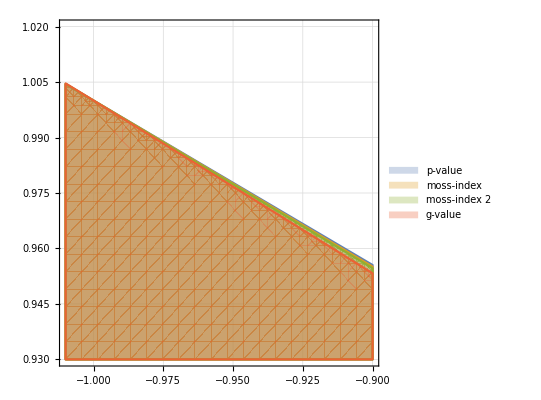

```mathematica
RegionPlot[
{
RCndsM14[baseMean, baseSigma, {2.2481, 0}],
RCndsM25[baseMean, baseSigma, {0.87, 5.52,1.37}],
RCndsM25[baseMean, baseSigma, {1.0, 3.82,3.62}],
RCndsM32[baseMean, baseSigma, {0.802, 1.0}]
},
{mean, -1.01, -0.9},
{sigma, 0.93, 1.02}, PlotLegends->{"p-value","moss-index","moss-index 2", "g-value" }
]
```

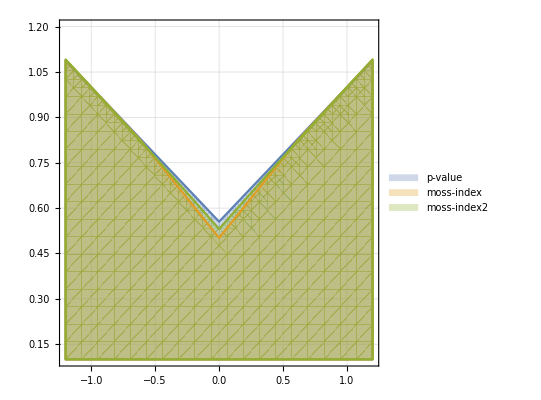

```mathematica
RegionPlot[
{
RCndsM14[baseMean, baseSigma, {2.2481, 0}],
RCndsM25[baseMean, baseSigma, {1.0, 3.82,3.62}],
RCndsM25[baseMean, baseSigma, {0.85, 5.52,1.37}]
},
{mean, -1.2, 1.2},
{sigma, 0.1, 1.2}, PlotLegends->{"p-value","moss-index", "moss-index2" }
]
```

#### Slopes

```mathematica
pS0 = 2.2481;
```

```mathematica
baseMean=-1.0; baseSigma = 1;
```

```mathematica
pS=pS0;
slope14=pS
```

2.2481

```mathematica
{pS, pL,pKsi}= {1.0, 3.82,3.62};
f=MossIndex[mean,σ,pS,pL, pKsi];
slope30=(  D[f,σ]/D[f, mean])/.{mean->baseMean,σ->  baseSigma}
```

2.2103

```mathematica
pS=0.83;
ksi=-(baseSigma*pS)^2*GIndex[baseMean,pS * baseSigma,0];
f=GIndex[mean,pS * σ,ksi];
slope30=(D[f,σ]/D[f, mean] )/.{mean->baseMean,σ->  baseSigma}
```

2.21188

### Traces

#### Traces data

```mathematica
tr1={"ship",{{-1.000000,1.000000},{-0.894437,0.992278},{-1.070607,0.984732},{-0.963687,0.977356},{-0.982136,0.970143},{-0.800236,0.963087},{-0.888873,0.956183},{-1.013609,0.949425},{-1.012100,0.942809},{-0.868843,0.936329},{-0.674679,0.929981},{-0.580934,0.923760},{-0.448763,0.917663},{-0.371069,0.911685},{-0.456196,0.905822},{-0.399668,0.900070},{-0.414427,0.894427},{-0.338780,0.888889},{-0.326282,0.883452},{-0.143229,0.878114},{-0.126695,0.872872},{-0.160286,0.867722},{-0.183958,0.862662},{-0.122599,0.857690},{-0.098340,0.852803},{-0.023336,0.847998},{-0.034049,0.843274},{-0.097499,0.838628},{0.020391,0.834058},{0.030830,0.829561},{-0.069281,0.825137},{0.015275,0.820783},{-0.078319,0.816497},{-0.007009,0.812277},{-0.060639,0.808122},{-0.072462,0.804030},{-0.059450,0.800000},{-0.051432,0.796030},{0.007351,0.792118},{-0.146573,0.788263},{-0.126497,0.784465},{-0.227228,0.780720},{-0.228313,0.777029},{-0.191746,0.773389},{-0.095127,0.769800},{-0.116955,0.766261},{-0.106486,0.762770},{-0.086372,0.759326},{-0.079592,0.755929},{-0.072680,0.752577},{0.025062,0.749269},{0.090589,0.746004},{0.074266,0.742781},{-0.085898,0.739600},{-0.088276,0.736460},{-0.006376,0.733359},{0.116417,0.730297},{0.130648,0.727273},{0.181562,0.724286},{0.138950,0.721336},{0.210849,0.718421},{0.141293,0.715542},{0.250255,0.712697},{0.279410,0.709885},{0.272455,0.707107},{0.242515,0.704361},{0.233310,0.701646},{0.232946,0.698963},{0.200979,0.696311},{0.253702,0.693688},{0.268808,0.691095},{0.373558,0.688530},{0.359356,0.685994},{0.328244,0.683486},{0.377522,0.681005},{0.455731,0.678551},{0.467368,0.676123},{0.443799,0.673722},{0.478835,0.671345},{0.508298,0.668994},{0.547937,0.666667},{0.423918,0.664364},{0.459609,0.662085},{0.373950,0.659829},{0.369442,0.657596},{0.307557,0.655386},{0.278085,0.653197},{0.337153,0.651031},{0.437752,0.648886},{0.438950,0.646762},{0.401765,0.644658},{0.487654,0.642575},{0.533639,0.640513},{0.534720,0.638470},{0.508035,0.636446},{0.432722,0.634441},{0.435013,0.632456},{0.460038,0.630488},{0.446861,0.628539},{0.485744,0.626608},{0.487091,0.624695},{0.483975,0.622799},{0.508890,0.620920},{0.555917,0.619059},{0.586497,0.617213},{0.567454,0.615385},{0.569576,0.613572},{0.477751,0.611775},{0.464865,0.609994},{0.476067,0.608229},{0.486493,0.606478},{0.533041,0.604743},{0.568444,0.603023},{0.550801,0.601317},{0.570752,0.599625},{0.624757,0.597948},{0.606705,0.596285},{0.627193,0.594635},{0.658164,0.592999},{0.782178,0.591377},{0.794640,0.589768},{0.761764,0.588172},{0.843919,0.586588},{0.882459,0.585018},{0.820316,0.583460},{0.839775,0.581914},{0.811306,0.580381},{0.784860,0.578860},{0.805684,0.577350},{0.848343,0.575853},{0.872594,0.574367},{0.919346,0.572892},{0.903049,0.571429},{0.934381,0.569976},{0.918963,0.568535},{0.945163,0.567105},{0.924549,0.565685},{0.901616,0.564276},{0.902250,0.562878},{0.879629,0.561490},{0.915453,0.560112},{0.907796,0.558744},{0.887813,0.557386},{0.916495,0.556038},{0.948959,0.554700},{0.964001,0.553372},{0.952197,0.552052},{0.944537,0.550743},{0.957412,0.549442},{0.942263,0.548151},{0.908739,0.546869},{0.958630,0.545595},{0.984503,0.544331},{1.028730,0.543075},{1.039112,0.541828},{1.034205,0.540590},{1.010907,0.539360},{1.016667,0.538138},{1.049518,0.536925},{1.099061,0.535720},{1.093005,0.534522},{1.097751,0.533333},{1.075891,0.532152},{1.028358,0.530979},{1.073584,0.529813},{1.089907,0.528655},{1.104219,0.527504},{1.102249,0.526361},{1.121441,0.525226},{1.112670,0.524097},{1.063810,0.522976},{1.115949,0.521862},{1.099425,0.520756},{1.160027,0.519656},{1.138516,0.518563},{1.119222,0.517477},{1.176417,0.516398},
{1.203268,0.515325}}};

tr2={"ship",{{-1.000000,1.000000},{-0.739508,0.992278},{-0.744479,0.984732},{-0.871848,0.977356},{-0.779518,0.970143},{-0.634249,0.963087},{-0.388693,0.956183},{-0.284854,0.949425},{-0.252119,0.942809},{-0.169194,0.936329},{-0.241819,0.929981},{-0.151756,0.923760},{0.013232,0.917663},{-0.036693,0.911685},{-0.095317,0.905822},{-0.008328,0.900070},{-0.074876,0.894427},{-0.071151,0.888889},{-0.166003,0.883452},{-0.167640,0.878114},{-0.182962,0.872872},{-0.342687,0.867722},{-0.094964,0.862662},{-0.070866,0.857690},{-0.088584,0.852803},{-0.123807,0.847998},{-0.039957,0.843274},{-0.047410,0.838628},{-0.091747,0.834058},{-0.067812,0.829561},{0.018459,0.825137},{0.137963,0.820783},{0.108413,0.816497},{0.267581,0.812277},{0.411106,0.808122},{0.417667,0.804030},{0.524030,0.800000},{0.532843,0.796030},{0.508977,0.792118},{0.465563,0.788263},{0.432023,0.784465},{0.549376,0.780720},{0.634638,0.777029},{0.592416,0.773389},{0.543695,0.769800},{0.641808,0.766261},{0.697811,0.762770},{0.758061,0.759326},{0.830312,0.755929},{0.873021,0.752577},{0.868744,0.749269},{0.912552,0.746004},{0.912490,0.742781},{1.027555,0.739600},{1.103932,0.736460},{1.160787,0.733359},{1.182250,0.730297},{1.200278,0.727273},{1.242253,0.724286},{1.323434,0.721336},{1.291069,0.718421},{1.315774,0.715542},{1.243259,0.712697},{1.224029,0.709885},{1.210895,0.707107},{1.261329,0.704361},{1.232509,0.701646},{1.147707,0.698963},{1.224160,0.696311},{1.195015,0.693688},{1.223665,0.691095},{1.256263,0.688530},{1.175264,0.685994},{1.234963,0.683486},{1.187551,0.681005},{1.078419,0.678551},{1.021756,0.676123},{1.022304,0.673722},{1.113735,0.671345},{1.003379,0.668994},{0.993174,0.666667},{1.032625,0.664364},{1.023308,0.662085},{0.978274,0.659829},{1.038696,0.657596},{0.994010,0.655386},{0.972637,0.653197},{0.992986,0.651031},{1.041419,0.648886},{0.976004,0.646762},{0.940562,0.644658},{0.871075,0.642575},{0.871245,0.640513},{0.831346,0.638470},{0.808971,0.636446},{0.902095,0.634441},{0.788674,0.632456},{0.878954,0.630488},{0.870950,0.628539},{0.872345,0.626608},{0.893417,0.624695},{0.866474,0.622799},{0.835349,0.620920},{0.773261,0.619059},{0.731756,0.617213},{0.674886,0.615385},{0.668682,0.613572},{0.681371,0.611775},{0.633306,0.609994},{0.587230,0.608229},{0.603759,0.606478},{0.594550,0.604743},{0.616681,0.603023},{0.584580,0.601317},{0.544326,0.599625},{0.587433,0.597948},{0.631997,0.596285},{0.607702,0.594635},{0.708046,0.592999},{0.727689,0.591377},{0.678377,0.589768},{0.634243,0.588172},{0.624303,0.586588},{0.728048,0.585018},{0.761339,0.583460},{0.791540,0.581914},{0.804911,0.580381},{0.811114,0.578860},{0.818476,0.577350},{0.876002,0.575853},{0.833827,0.574367},{0.848314,0.572892},{0.784698,0.571429},{0.755152,0.569976},{0.780006,0.568535},{0.741841,0.567105},{0.751311,0.565685},{0.744086,0.564276},{0.720281,0.562878},{0.714218,0.561490},{0.696680,0.560112},{0.684608,0.558744},{0.651595,0.557386},{0.640850,0.556038},{0.675268,0.554700},{0.714536,0.553372},{0.753319,0.552052},{0.714736,0.550743},{0.810273,0.549442},{0.801123,0.548151},{0.837694,0.546869},{0.880760,0.545595},{0.894529,0.544331},{0.904928,0.543075},{0.945785,0.541828},{0.969897,0.540590},{0.955036,0.539360},{0.908374,0.538138},{0.961938,0.536925},{0.939905,0.535720},{0.924100,0.534522},{0.899602,0.533333},{0.942562,0.532152},{0.930614,0.530979},{0.970732,0.529813},{0.983212,0.528655},{1.009788,0.527504},{1.058769,0.526361},{1.083854,0.525226},{1.053820,0.524097},{1.008650,0.522976},{1.035785,0.521862},{1.072995,0.520756},{1.101971,0.519656},{1.067500,0.518563},{1.098670,0.517477},{1.132844,0.516398},{1.139712,0.515325},{1.111141,0.514259},{1.123680,0.513200},{1.107841,0.512148},{1.147769,0.511101},{1.091179,0.510061},{1.160081,0.509028},{1.128112,0.508001},{1.165482,0.506979},
{1.214434,0.505964}}};
```

```mathematica
stopTraces={
{"stop",{{-1.000000,1.000000},{-0.894256,0.992278},{-0.854128,0.984732},{-1.041941,0.977356},{-0.885074,0.970143},{-0.925162,0.963087},{-0.776741,0.956183},{-0.690357,0.949425},{-0.846815,0.942809},{-0.782397,0.936329},{-0.654921,0.929981},{-0.579800,0.923760},{-0.584092,0.917663},{-0.590147,0.911685},{-0.659894,0.905822},{-0.675198,0.900070},{-0.647647,0.894427},{-0.638498,0.888889},{-0.629995,0.883452},{-0.689343,0.878114},{-0.751355,0.872872},{-0.835855,0.867722},{-0.880613,0.862662},{-0.996943,0.857690}}},{"stop",{{-1.000000,1.000000},{-1.028357,0.992278},{-1.086179,0.984732},{-1.055206,0.977356},{-1.011501,0.970143},{-1.024385,0.963087},{-0.939608,0.956183},{-0.895195,0.949425},{-0.922705,0.942809},{-0.840196,0.936329},{-0.879640,0.929981},{-0.767181,0.923760},{-0.655435,0.917663},{-0.562910,0.911685},{-0.541634,0.905822},{-0.603781,0.900070},{-0.663667,0.894427},{-0.603361,0.888889},{-0.594274,0.883452},{-0.541782,0.878114},{-0.548920,0.872872},{-0.566718,0.867722},{-0.549991,0.862662},{-0.730588,0.857690},{-0.741141,0.852803},{-0.732892,0.847998},{-0.642731,0.843274},{-0.584947,0.838628},{-0.571325,0.834058},{-0.528177,0.829561},{-0.666413,0.825137},{-0.677094,0.820783},{-0.706463,0.816497},{-0.647190,0.812277},{-0.586859,0.808122},{-0.762498,0.804030},{-0.704090,0.800000},{-0.704551,0.796030},{-0.574065,0.792118},{-0.582338,0.788263},{-0.595142,0.784465},{-0.597777,0.780720},{-0.661319,0.777029},{-0.695485,0.773389},{-0.636441,0.769800},{-0.577976,0.766261},{-0.577782,0.762770},{-0.596125,0.759326},{-0.642727,0.755929},{-0.626615,0.752577},{-0.586670,0.749269},{-0.477109,0.746004},{-0.413426,0.742781},{-0.415964,0.739600},{-0.398094,0.736460},{-0.467620,0.733359},{-0.501172,0.730297},{-0.356424,0.727273},{-0.360904,0.724286},{-0.314436,0.721336},{-0.270444,0.718421},{-0.274574,0.715542},{-0.302008,0.712697},{-0.226052,0.709885},{-0.040987,0.707107},{-0.169652,0.704361},{-0.215448,0.701646},{-0.193885,0.698963},{-0.188744,0.696311},{-0.136065,0.693688},{-0.188768,0.691095},{-0.127564,0.688530},{-0.153549,0.685994},{-0.194333,0.683486},{-0.240091,0.681005},{-0.202705,0.678551},{-0.140372,0.676123},{-0.110355,0.673722},{-0.184502,0.671345},{-0.132306,0.668994},{-0.225169,0.666667},{-0.257923,0.664364},{-0.208437,0.662085},{-0.198834,0.659829},{-0.248503,0.657596},{-0.200563,0.655386},{-0.145222,0.653197},{-0.100419,0.651031},{-0.256411,0.648886},{-0.308386,0.646762},{-0.317500,0.644658},{-0.292043,0.642575},{-0.317821,0.640513},{-0.333766,0.638470},{-0.399892,0.636446},{-0.424137,0.634441},{-0.505550,0.632456},{-0.577050,0.630488},{-0.671560,0.628539},{-0.687483,0.626608}}},{"stop",{{-1.000000,1.000000},{-0.913519,0.992278},{-0.792935,0.984732},{-0.720436,0.977356},{-0.641106,0.970143},{-0.585982,0.963087},{-0.783442,0.956183},{-0.847665,0.949425},{-1.017496,0.942809},{-0.856579,0.936329},{-0.892259,0.929981},{-0.838726,0.923760},{-0.762238,0.917663},{-0.773349,0.911685},{-0.597429,0.905822},{-0.615080,0.900070},{-0.424986,0.894427},{-0.336043,0.888889},{-0.273566,0.883452},{-0.184372,0.878114},{-0.155319,0.872872},{-0.201403,0.867722},{-0.113456,0.862662},{-0.242175,0.857690},{-0.340412,0.852803},{-0.153309,0.847998},{-0.236992,0.843274},{-0.276864,0.838628},{-0.254076,0.834058},{-0.244718,0.829561},{-0.341953,0.825137},{-0.238237,0.820783},{-0.378174,0.816497},{-0.166357,0.812277},{-0.164491,0.808122},{-0.273830,0.804030},{-0.396380,0.800000},{-0.429605,0.796030},{-0.381167,0.792118},{-0.431270,0.788263},{-0.455749,0.784465},{-0.510841,0.780720},{-0.321586,0.777029},{-0.318726,0.773389},{-0.351642,0.769800},{-0.292898,0.766261},{-0.242891,0.762770},{-0.047494,0.759326},{-0.051635,0.755929},{0.004101,0.752577},{0.059935,0.749269},{0.077188,0.746004},{0.062467,0.742781},{-0.010140,0.739600},{-0.028800,0.736460},{0.016826,0.733359},{0.066827,0.730297},{0.034079,0.727273},{0.002085,0.724286},{-0.004002,0.721336},{0.003827,0.718421},{-0.012286,0.715542},{-0.013325,0.712697},{-0.029070,0.709885},{0.054049,0.707107},{0.070641,0.704361},{0.141972,0.701646},{0.173192,0.698963},{0.118978,0.696311},{0.092787,0.693688},{0.118317,0.691095},{0.071435,0.688530},{0.100819,0.685994},{0.071345,0.683486},{0.025707,0.681005},{0.015603,0.678551},{-0.030008,0.676123},{-0.036012,0.673722},{-0.061532,0.671345},{-0.103304,0.668994},{-0.064573,0.666667},{-0.085372,0.664364},{0.004528,0.662085},{-0.049813,0.659829},{0.017902,0.657596},{0.015917,0.655386},{-0.050300,0.653197},{0.000266,0.651031},{0.021283,0.648886},{0.000405,0.646762},{-0.065494,0.644658},{0.009299,0.642575},{0.008501,0.640513},{-0.019023,0.638470},{-0.079356,0.636446},{-0.050489,0.634441},{-0.042808,0.632456},{-0.024461,0.630488},{0.072413,0.628539},{0.097913,0.626608},{0.201700,0.624695},{0.149676,0.622799},{0.158642,0.620920},{0.128443,0.619059},{0.102622,0.617213},{0.076279,0.615385},{0.155517,0.613572},{0.233876,0.611775},{0.236149,0.609994},{0.186699,0.608229},{0.289294,0.606478},{0.304099,0.604743},{0.277692,0.603023},{0.319132,0.601317},{0.375549,0.599625},{0.359277,0.597948},{0.334983,0.596285},{0.334255,0.594635},{0.269004,0.592999},{0.244222,0.591377},{0.214553,0.589768},{0.226446,0.588172},{0.242133,0.586588},{0.235806,0.585018},{0.220749,0.583460},{0.183126,0.581914},{0.223738,0.580381},{0.197688,0.578860},{0.171744,0.577350},{0.206124,0.575853},{0.238790,0.574367},{0.196703,0.572892},{0.198412,0.571429},{0.287197,0.569976},{0.271069,0.568535},{0.308454,0.567105},{0.307202,0.565685},{0.359699,0.564276},{0.401458,0.562878},{0.471815,0.561490},{0.458048,0.560112},{0.423971,0.558744},{0.430718,0.557386},{0.427714,0.556038},{0.342874,0.554700},{0.315948,0.553372},{0.323314,0.552052},{0.384007,0.550743},{0.431262,0.549442},{0.411243,0.548151},{0.401733,0.546869},{0.395433,0.545595},{0.386275,0.544331},{0.406957,0.543075},{0.403512,0.541828},{0.429953,0.540590},{0.535441,0.539360},{0.514706,0.538138},{0.511836,0.536925},{0.536063,0.535720},{0.471420,0.534522},{0.514647,0.533333},{0.515834,0.532152},{0.528046,0.530979},{0.548743,0.529813},{0.529052,0.528655},{0.483155,0.527504},{0.506770,0.526361},{0.500619,0.525226},{0.497723,0.524097},{0.455742,0.522976},{0.452749,0.521862},{0.438794,0.520756},{0.459013,0.519656},{0.450717,0.518563},{0.411538,0.517477},{0.378010,0.516398},{0.360562,0.515325},{0.338330,0.514259},{0.326489,0.513200},{0.333933,0.512148},{0.346051,0.511101},{0.328508,0.510061},{0.361978,0.509028},{0.335162,0.508001},{0.326508,0.506979},{0.303255,0.505964},{0.298376,0.504956},{0.303285,0.503953},{0.286363,0.502956},{0.291953,0.501965},{0.297742,0.500979},{0.262586,0.500000},{0.304579,0.499026},{0.281903,0.498058},{0.267917,0.497096},{0.268750,0.496139},{0.261043,0.495188},{0.297280,0.494242},{0.315040,0.493301},{0.282176,0.492366},{0.294436,0.491436},{0.240741,0.490511},{0.280368,0.489592},{0.308271,0.488678},{0.339773,0.487769},{0.361549,0.486864},{0.382437,0.485965},{0.368828,0.485071},{0.336227,0.484182},{0.334386,0.483298},{0.338670,0.482418},{0.329080,0.481543},{0.338967,0.480673},{0.354513,0.479808},{0.324240,0.478947},{0.324200,0.478091},{0.295649,0.477240},{0.260624,0.476393},{0.265447,0.475551},{0.210497,0.474713},{0.214107,0.473879},{0.243754,0.473050},{0.276135,0.472225},{0.268900,0.471405},{0.275375,0.470588},{0.257162,0.469776},{0.258387,0.468968},{0.285150,0.468165},{0.255293,0.467365},{0.218846,0.466569},{0.236093,0.465778},{0.218390,0.464991},{0.214821,0.464207},{0.182794,0.463428},{0.154062,0.462652},{0.167035,0.461880},{0.158214,0.461112},{0.152261,0.460348},{0.131200,0.459588},{0.104412,0.458831},{0.076504,0.458079},{0.061494,0.457330},{0.084036,0.456584},{0.100073,0.455842},{0.111607,0.455104},{0.122491,0.454369},{0.102110,0.453638},{0.092149,0.452911},{0.096460,0.452187},{0.121856,0.451466},{0.086258,0.450749},{0.100529,0.450035},{0.067416,0.449325},{0.090884,0.448618},{0.099499,0.447914},{0.074288,0.447214},{0.011302,0.446516},{-0.000482,0.445823},{-0.066744,0.445132},{-0.059149,0.444444},{-0.066243,0.443760},{-0.093914,0.443079},{-0.063741,0.442401},{-0.054203,0.441726},{-0.030802,0.441054},{-0.024299,0.440386},{-0.050871,0.439720},{-0.029656,0.439057},{-0.035704,0.438397},{-0.075415,0.437741},{-0.121601,0.437087},{-0.128841,0.436436},{-0.127192,0.435788},{-0.149216,0.435143},{-0.113834,0.434500},{-0.101927,0.433861},{-0.105436,0.433224},{-0.110667,0.432590},{-0.111884,0.431959},{-0.088798,0.431331},{-0.105160,0.430706},{-0.144907,0.430083},{-0.104521,0.429463},{-0.126429,0.428845},{-0.108568,0.428230},{-0.136362,0.427618},{-0.105642,0.427008},{-0.111421,0.426401},{-0.122764,0.425797},{-0.112278,0.425195},{-0.080428,0.424596},{-0.091951,0.423999},{-0.111064,0.423405},{-0.099473,0.422813},{-0.108044,0.422224},{-0.102095,0.421637},{-0.136181,0.421053},{-0.142626,0.420471},{-0.125760,0.419891},{-0.153946,0.419314},{-0.165801,0.418739},{-0.175096,0.418167},{-0.197692,0.417597},{-0.200634,0.417029},{-0.212670,0.416463},{-0.162400,0.415900},{-0.131809,0.415339},{-0.150894,0.414781},{-0.130074,0.414224},{-0.123494,0.413670},{-0.131902,0.413118},{-0.137045,0.412568},{-0.146447,0.412021},{-0.144703,0.411476},{-0.128570,0.410932},{-0.102308,0.410391},{-0.132706,0.409852},{-0.097330,0.409316},{-0.098890,0.408781},{-0.091899,0.408248},{-0.059740,0.407718},{-0.050103,0.407189},{-0.051003,0.406663},{-0.056244,0.406138},{-0.057449,0.405616},{-0.088611,0.405096},{-0.100468,0.404577},{-0.136810,0.404061},{-0.151696,0.403547},{-0.207183,0.403034},{-0.246258,0.402524},{-0.245774,0.402015},{-0.264538,0.401508},{-0.308700,0.401004},{-0.310590,0.400501},{-0.313765,0.400000},{-0.288891,0.399501},{-0.320903,0.399004},{-0.280824,0.398508},{-0.295616,0.398015},{-0.264653,0.397523},{-0.285668,0.397033},{-0.257773,0.396545},{-0.243751,0.396059},{-0.236789,0.395575},{-0.227890,0.395092},{-0.202038,0.394611},{-0.178946,0.394132},{-0.178733,0.393654},{-0.204730,0.393179},{-0.205300,0.392705},{-0.222973,0.392232},{-0.249392,0.391762},{-0.241149,0.391293},{-0.226219,0.390826},{-0.229270,0.390360},{-0.224068,0.389896},{-0.191934,0.389434},{-0.168660,0.388973},{-0.157585,0.388514},{-0.170968,0.388057},{-0.170049,0.387601},{-0.175632,0.387147},{-0.187987,0.386695},{-0.205153,0.386244},{-0.193438,0.385794},{-0.201680,0.385346},{-0.203807,0.384900},{-0.201950,0.384455},{-0.221071,0.384012},{-0.231110,0.383571},{-0.235911,0.383131},{-0.235574,0.382692},{-0.224163,0.382255},{-0.227239,0.381819},{-0.221011,0.381385},{-0.234718,0.380952},{-0.240080,0.380521},{-0.240099,0.380091},{-0.247325,0.379663},{-0.276837,0.379236},{-0.265050,0.378811},{-0.281644,0.378387},{-0.292035,0.377964},{-0.321820,0.377543},{-0.343849,0.377124},{-0.347832,0.376705},{-0.339824,0.376288},{-0.336236,0.375873},{-0.315829,0.375459},{-0.325223,0.375046},{-0.326660,0.374634},{-0.310775,0.374224},{-0.314543,0.373815},{-0.317632,0.373408},{-0.342937,0.373002},{-0.339790,0.372597},{-0.341625,0.372194},{-0.349581,0.371792},{-0.357793,0.371391},{-0.371937,0.370991},{-0.350501,0.370593},{-0.364953,0.370196},{-0.346310,0.369800},{-0.360600,0.369406},{-0.346921,0.369012},{-0.375220,0.368621},{-0.398744,0.368230}}},{"stop",{{-1.000000,1.000000},{-0.865723,0.992278},{-0.825282,0.984732},{-0.587401,0.977356},{-0.519317,0.970143},{-0.478280,0.963087},{-0.395469,0.956183},{-0.363228,0.949425},{-0.362172,0.942809},{-0.431426,0.936329},{-0.441670,0.929981},{-0.358179,0.923760},{-0.243844,0.917663},{-0.409202,0.911685},{-0.367411,0.905822},{-0.272988,0.900070},{-0.334613,0.894427},{-0.217624,0.888889},{-0.122365,0.883452},{-0.275352,0.878114},{-0.254086,0.872872},{-0.197334,0.867722},{-0.126115,0.862662},{0.020947,0.857690},{-0.131696,0.852803},{-0.112806,0.847998},{-0.284680,0.843274},{-0.173981,0.838628},{-0.172382,0.834058},{-0.237304,0.829561},{-0.278864,0.825137},{-0.465802,0.820783},{-0.529336,0.816497},{-0.610800,0.812277},{-0.701539,0.808122},{-0.690409,0.804030},{-0.699202,0.800000},{-0.853205,0.796030},{-0.851960,0.792118},{-0.760663,0.788263},{-0.803130,0.784465},{-0.724458,0.780720},{-0.662956,0.777029},{-0.507522,0.773389},{-0.566147,0.769800},{-0.559703,0.766261},{-0.708735,0.762770},{-0.679576,0.759326},{-0.698756,0.755929},{-0.626868,0.752577},{-0.635360,0.749269},{-0.631015,0.746004},{-0.556248,0.742781},{-0.678407,0.739600},{-0.569131,0.736460},{-0.628790,0.733359},{-0.719832,0.730297},{-0.701128,0.727273},{-0.799047,0.724286}}},{"stop",{{-1.000000,1.000000},{-1.065184,0.992278},{-0.894549,0.984732},{-0.950441,0.977356},{-1.061377,0.970143},{-0.887411,0.963087},{-0.955136,0.956183},{-0.794022,0.949425},{-0.735827,0.942809},{-0.608064,0.936329},{-0.684151,0.929981},{-0.577198,0.923760},{-0.321117,0.917663},{-0.268269,0.911685},{-0.184121,0.905822},{-0.076780,0.900070},{-0.268400,0.894427},{-0.277475,0.888889},{-0.178606,0.883452},{-0.166563,0.878114},{-0.189824,0.872872},{-0.133766,0.867722},{-0.039579,0.862662},{0.019864,0.857690},{0.105003,0.852803},{0.198231,0.847998},{0.128916,0.843274},{0.063278,0.838628},{0.234763,0.834058},{0.177313,0.829561},{0.267950,0.825137},{0.107829,0.820783},{0.175877,0.816497},{0.221667,0.812277},{0.154360,0.808122},{0.077291,0.804030},{0.080080,0.800000},{-0.037266,0.796030},{0.038016,0.792118},{-0.001295,0.788263},{0.112980,0.784465},{0.086829,0.780720},{0.027397,0.777029},{-0.074813,0.773389},{-0.094928,0.769800},{-0.099522,0.766261},{-0.163195,0.762770},{-0.252747,0.759326},{-0.134381,0.755929},{-0.035555,0.752577},{-0.049810,0.749269},{-0.033135,0.746004},{0.000445,0.742781},{-0.056340,0.739600},{-0.049349,0.736460},{-0.045521,0.733359},{-0.086214,0.730297},{-0.109750,0.727273},{-0.182413,0.724286},{-0.153201,0.721336},{-0.115703,0.718421},{-0.223971,0.715542},{-0.137516,0.712697},{-0.102735,0.709885},{-0.186186,0.707107},{-0.094539,0.704361},{-0.187834,0.701646},{-0.191332,0.698963},{-0.243167,0.696311},{-0.289665,0.693688},{-0.289632,0.691095},{-0.263288,0.688530},{-0.264953,0.685994},{-0.404251,0.683486},{-0.358295,0.681005},{-0.346884,0.678551},{-0.362410,0.676123},{-0.320764,0.673722},{-0.268326,0.671345},{-0.137218,0.668994},{-0.087418,0.666667},{-0.144949,0.664364},{-0.113991,0.662085},{-0.174512,0.659829},{-0.137780,0.657596},{0.025672,0.655386},{-0.019621,0.653197},{0.019402,0.651031},{0.008747,0.648886},{0.010340,0.646762},{-0.091302,0.644658},{-0.215708,0.642575},{-0.195360,0.640513},{-0.194545,0.638470},{-0.202531,0.636446},{-0.254772,0.634441},{-0.219467,0.632456},{-0.235287,0.630488},{-0.299540,0.628539},{-0.277251,0.626608},{-0.248569,0.624695},{-0.198650,0.622799},{-0.166722,0.620920},{-0.228745,0.619059},{-0.181844,0.617213},{-0.177662,0.615385},{-0.212833,0.613572},{-0.247137,0.611775},{-0.194105,0.609994},{-0.254887,0.608229},{-0.223729,0.606478},{-0.198031,0.604743},{-0.184816,0.603023},{-0.246039,0.601317},{-0.230162,0.599625},{-0.277018,0.597948},{-0.219620,0.596285},{-0.247558,0.594635},{-0.253425,0.592999},{-0.223235,0.591377},{-0.223138,0.589768},{-0.292359,0.588172},{-0.201367,0.586588},{-0.150232,0.585018},{-0.244114,0.583460},{-0.209658,0.581914},{-0.181856,0.580381},{-0.211679,0.578860},{-0.173267,0.577350},{-0.184957,0.575853},{-0.187560,0.574367},{-0.252790,0.572892},{-0.213589,0.571429},{-0.253471,0.569976},{-0.224933,0.568535},{-0.242997,0.567105},{-0.267809,0.565685},{-0.306598,0.564276},{-0.285046,0.562878},{-0.262370,0.561490},{-0.293814,0.560112},{-0.389982,0.558744},{-0.354568,0.557386},{-0.341436,0.556038},{-0.313019,0.554700},{-0.278688,0.553372},{-0.224429,0.552052},{-0.153868,0.550743},{-0.198644,0.549442},{-0.198819,0.548151},{-0.255492,0.546869},{-0.272591,0.545595},{-0.273521,0.544331},{-0.308313,0.543075},{-0.399093,0.541828},{-0.452794,0.540590},{-0.474375,0.539360},{-0.435157,0.538138},{-0.376249,0.536925},{-0.396227,0.535720},{-0.395147,0.534522},{-0.377149,0.533333},{-0.325573,0.532152},{-0.369018,0.530979},{-0.340967,0.529813},{-0.289728,0.528655},{-0.352339,0.527504},{-0.280114,0.526361},{-0.324306,0.525226},{-0.325537,0.524097},{-0.439823,0.522976},{-0.468368,0.521862},{-0.454813,0.520756},{-0.417209,0.519656},{-0.477577,0.518563},{-0.512823,0.517477},{-0.531617,0.516398},{-0.493678,0.515325},{-0.494750,0.514259},{-0.445462,0.513200},{-0.425054,0.512148},{-0.477491,0.511101},{-0.447558,0.510061},{-0.409144,0.509028},{-0.426941,0.508001},{-0.429975,0.506979},{-0.418928,0.505964},{-0.409177,0.504956},{-0.410239,0.503953},{-0.401989,0.502956},{-0.375032,0.501965},{-0.346343,0.500979},{-0.296109,0.500000},{-0.251212,0.499026},{-0.221500,0.498058},{-0.258815,0.497096},{-0.216750,0.496139},{-0.186819,0.495188},{-0.194628,0.494242},{-0.190544,0.493301},{-0.222884,0.492366},{-0.196009,0.491436},{-0.239576,0.490511},{-0.219411,0.489592},{-0.229739,0.488678},{-0.230038,0.487769},{-0.229122,0.486864},{-0.210156,0.485965},{-0.202477,0.485071},{-0.217959,0.484182},{-0.183630,0.483298},{-0.163847,0.482418},{-0.158629,0.481543},{-0.188165,0.480673},{-0.256285,0.479808},{-0.267184,0.478947},{-0.260643,0.478091},{-0.305103,0.477240},{-0.342916,0.476393},{-0.324330,0.475551},{-0.355762,0.474713},{-0.353749,0.473879},{-0.359606,0.473050},{-0.329622,0.472225},{-0.318932,0.471405},{-0.356211,0.470588},{-0.344768,0.469776},{-0.338549,0.468968},{-0.356328,0.468165},{-0.349790,0.467365},{-0.373498,0.466569},{-0.422332,0.465778},{-0.416328,0.464991},{-0.387280,0.464207},{-0.423800,0.463428},{-0.499218,0.462652}}},{"stop",{{-1.000000,1.000000},{-0.972459,0.992278},{-0.962638,0.984732},{-0.932294,0.977356},{-0.808895,0.970143},{-0.668381,0.963087},{-0.643302,0.956183},{-0.644306,0.949425},{-0.630622,0.942809},{-0.823474,0.936329},{-0.906208,0.929981},{-0.802635,0.923760},{-0.688392,0.917663},{-0.710020,0.911685},{-0.706680,0.905822},{-0.570990,0.900070},{-0.602085,0.894427},{-0.571293,0.888889},{-0.588539,0.883452},{-0.707313,0.878114},{-0.700926,0.872872},{-0.815575,0.867722},{-0.795681,0.862662},{-0.645938,0.857690},{-0.429951,0.852803},{-0.486530,0.847998},{-0.407009,0.843274},{-0.434674,0.838628},{-0.587052,0.834058},{-0.588928,0.829561},{-0.410328,0.825137},{-0.412029,0.820783},{-0.415294,0.816497},{-0.465636,0.812277},{-0.389577,0.808122},{-0.368181,0.804030},{-0.510454,0.800000},{-0.507928,0.796030},{-0.444733,0.792118},{-0.510318,0.788263},{-0.431451,0.784465},{-0.423452,0.780720},{-0.343877,0.777029},{-0.339332,0.773389},{-0.354306,0.769800},{-0.317388,0.766261},{-0.226802,0.762770},{-0.152920,0.759326},{-0.236670,0.755929},{-0.197533,0.752577},{-0.187595,0.749269},{-0.142081,0.746004},{-0.134937,0.742781},{-0.188916,0.739600},{-0.233945,0.736460},{-0.281522,0.733359},{-0.200900,0.730297},{-0.144925,0.727273},{-0.199608,0.724286},{-0.198432,0.721336},{-0.183218,0.718421},{-0.081727,0.715542},{-0.213111,0.712697},{-0.235715,0.709885},{-0.300235,0.707107},{-0.190738,0.704361},{-0.154976,0.701646},{-0.177110,0.698963},{-0.234584,0.696311},{-0.216239,0.693688},{-0.200709,0.691095},{-0.240794,0.688530},{-0.235947,0.685994},{-0.261453,0.683486},{-0.283695,0.681005},{-0.308177,0.678551},{-0.245544,0.676123},{-0.190172,0.673722},{-0.185917,0.671345},{-0.189684,0.668994},{-0.168433,0.666667},{-0.234212,0.664364},{-0.305645,0.662085},{-0.269026,0.659829},{-0.304190,0.657596},{-0.304886,0.655386},{-0.306160,0.653197},{-0.383526,0.651031},{-0.448766,0.648886},{-0.562598,0.646762},{-0.614027,0.644658},{-0.608732,0.642575},{-0.581826,0.640513},{-0.571074,0.638470},{-0.555058,0.636446},{-0.545025,0.634441},{-0.553755,0.632456},{-0.566510,0.630488},{-0.584019,0.628539},{-0.607627,0.626608},{-0.638787,0.624695},{-0.614802,0.622799},{-0.528223,0.620920},{-0.511110,0.619059},{-0.610981,0.617213},{-0.574535,0.615385},{-0.602008,0.613572},{-0.545438,0.611775},{-0.570880,0.609994},{-0.587568,0.608229},{-0.577159,0.606478},{-0.593775,0.604743},{-0.594538,0.603023},{-0.624755,0.601317},{-0.542595,0.599625},{-0.527378,0.597948},{-0.531323,0.596285},{-0.556594,0.594635},{-0.487012,0.592999},{-0.579153,0.591377},{-0.635090,0.589768},{-0.656037,0.588172}}}
};

tr3={"ship",{{-1.000000,1.000000},{-0.951771,0.992278},{-0.960027,0.984732},{-0.991817,0.977356},{-0.866113,0.970143},{-0.862036,0.963087},{-0.906765,0.956183},{-0.862055,0.949425},{-0.736540,0.942809},{-0.568852,0.936329},{-0.595833,0.929981},{-0.378807,0.923760},{-0.183475,0.917663},{-0.165586,0.911685},{-0.020035,0.905822},{-0.000193,0.900070},{-0.022291,0.894427},{-0.069291,0.888889},{-0.103681,0.883452},{0.052840,0.878114},{0.167930,0.872872},{0.121840,0.867722},{0.067679,0.862662},{0.197606,0.857690},{0.274173,0.852803},{0.355576,0.847998},{0.451442,0.843274},{0.510105,0.838628},{0.510201,0.834058},{0.569660,0.829561},{0.574652,0.825137},{0.721323,0.820783},{0.819783,0.816497},{0.893837,0.812277},{0.924203,0.808122},{0.950191,0.804030},{1.005235,0.800000},{1.107766,0.796030},{1.071843,0.792118},{1.105248,0.788263},{1.020700,0.784465},{1.000831,0.780720},{0.988335,0.777029},{1.052466,0.773389},{1.020944,0.769800},{0.922190,0.766261},{1.017197,0.762770},{0.985341,0.759326},{1.022682,0.755929},{1.064585,0.752577},{0.970807,0.749269},{1.044864,0.746004},{0.991248,0.742781},{0.864414,0.739600},{0.800130,0.736460},{0.803763,0.733359},{0.914889,0.730297},{0.787214,0.727273},{0.778034,0.724286},{0.827374,0.721336},{0.819136,0.718421},{0.768876,0.715542},{0.842569,0.712697},{0.792736,0.709885},{0.770304,0.707107},{0.796726,0.704361},{0.855892,0.701646},{0.781925,0.698963},{0.743057,0.696311},{0.664563,0.693688},{0.667298,0.691095},{0.623396,0.688530},{0.599911,0.685994},{0.710489,0.683486},{0.581341,0.681005},{0.688361,0.678551},{0.681414,0.676123},{0.685317,0.673722},{0.711909,0.671345},{0.683024,0.668994},{0.649343,0.666667},{0.580038,0.664364},{0.534516,0.662085},{0.471383,0.659829},{0.466534,0.657596},{0.483349,0.655386},{0.430443,0.653197},{0.379880,0.651031},{0.401044,0.648886},{0.392707,0.646762},{0.420176,0.644658},{0.385647,0.642575},{0.341847,0.640513},{0.393134,0.638470},{0.445977,0.636446},{0.420329,0.634441},{0.536475,0.632456},{0.560697,0.630488},{0.506541,0.628539},{0.458323,0.626608},{0.448936,0.624695},{0.568384,0.622799},{0.607854,0.620920},{0.643751,0.619059},{0.660546,0.617213},{0.669201,0.615385},{0.679134,0.613572},{0.745656,0.611775},{0.699620,0.609994},{0.717496,0.608229},{0.647356,0.606478},{0.615642,0.604743},{0.645153,0.603023},{0.603760,0.601317},{0.615926,0.599625},{0.609314,0.597948},{0.584089,0.596285},{0.578778,0.594635},{0.560598,0.592999},{0.548547,0.591377},{0.513051,0.589768},{0.502498,0.588172},{0.542448,0.586588},{0.587759,0.585018},{0.632465,0.583460},{0.590736,0.581914},{0.698689,0.580381},{0.689768,0.578860},{0.731805,0.577350},{0.781019,0.575853},{0.797551,0.574367},{0.810304,0.572892},{0.856911,0.571429},{0.884844,0.569976},{0.869434,0.568535},{0.818714,0.567105},{0.879285,0.565685},{0.855916,0.564276},{0.839466,0.562878},{0.813387,0.561490},{0.862057,0.560112},{0.849869,0.558744},{0.895311,0.557386},{0.910127,0.556038},{0.940506,0.554700},{0.995612,0.553372},{1.024261,0.552052},{0.992010,0.550743},{0.943074,0.549442},{0.973945,0.548151},{1.015893,0.546869},{1.048720,0.545595},{1.011602,0.544331},{1.046805,0.543075},{1.085277,0.541828},{1.093661,0.540590},{1.063048,0.539360},{1.077657,0.538138},{1.061057,0.536925},{1.105732,0.535720},{1.044366,0.534522},{1.120807,0.533333},{1.086490,0.532152},{1.128252,0.530979},{1.182676,0.529813},{1.184629,0.528655},{1.157560,0.527504},{1.159602,0.526361},{1.179218,0.525226},{1.206345,0.524097},{1.233699,0.522976}}};
```

#### Plots

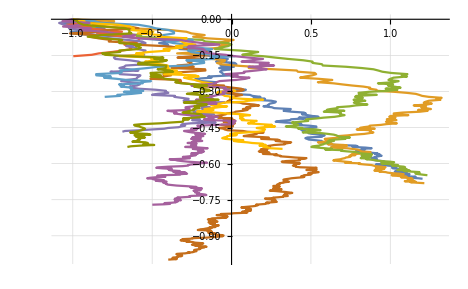

```mathematica
traces = Join[{tr1, tr2, tr3}, stopTraces];
TrTrace[l_]:={#⟦1⟧,Log[#⟦2⟧]}&/@l;
ListPlot[
(TrTrace[#⟦2⟧])&/@traces,Joined->True
]
```

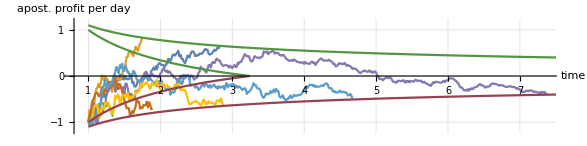

```mathematica
stopTraces2=stopTraces⟦⟧;
traces = Join[{tr1, tr2}, stopTraces];
TrTrace[l_]:={1/(#⟦2⟧)^2, #⟦1⟧}&/@l;
FilterTrace[l_]:=TakeWhile[l, #⟦1⟧≥ -1.1#⟦2⟧ && #⟦1⟧≤ 1.1#⟦2⟧ &];

tt=Range[1.0, 8,0.001];
g=ListPlot[
(TrTrace[FilterTrace[#⟦2⟧]])&/@traces,Joined->True,AspectRatio->1/4,
PlotRange->{{0.8,Automatic},{-1.2,1.2}},
AxesLabel-> {"time", "apost. profit per day"}
];
gStop = ListPlot[{#, -1.1/Sqrt[#]}&/@ tt,Joined->True,AspectRatio->1/4,PlotStyle->RGBColor[0.59,0.26,0.32]];
gShip = ListPlot[{#, 1.1/Sqrt[#]}&/@ tt,Joined->True,AspectRatio->1/4,
PlotStyle->RGBColor[0.32,0.59,0.26]];

gStop14 = ListPlot[TakeWhile[{#, -pS0(1/Sqrt[#]-1) -1}&/@ tt,#⟦2⟧≤ 0&],Joined->True,AspectRatio->1/4,PlotStyle->RGBColor[0.59,0.26,0.32]];
gShip14 = ListPlot[TakeWhile[{#, pS0(1/Sqrt[#]-1)+1}&/@ tt,#[[2]]≥ 0&],Joined->True,AspectRatio->1/4,
PlotStyle->RGBColor[0.32,0.59,0.26]];

Show[g,gStop,gShip, gStop14, gShip14]
```